```mathematica
putoa[p_, u_]:=√(p/u)
```

Need to run initialization cells of Comparing_models.nb first

## Running

```mathematica
putoa[100, 0.01]
```

100.

```mathematica
ga = 20
gb = 1/0.414 ga
gc = 60
```

20

48.3092

600

```mathematica
u=0.1;
sol = generalsolver2[0.0, u, putoa[100, u], 0.0, 11.5, 0.0, phogarray[ga, gb, gc, 5], 20];1;
```

```mathematica
putoa[100, 0.1]
```

31.6228

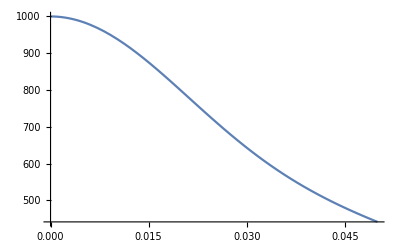

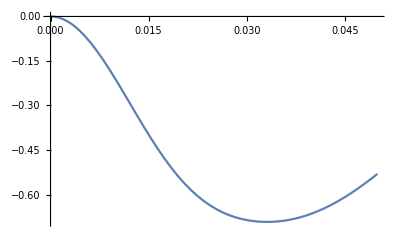

```mathematica
tmax2=0.05;
Plot[
{
Re@bd2b2[ga, gb, t]/.sol
},
{t, 0, tmax2}, PlotRange->All
]

Plot[
{
Re@Qb2[ga, gb, t]/.sol
},
{t, 0, tmax2}, PlotRange->All
]
```

TODO: Let’s check (partial) scaling

```mathematica
u=0.1;
sol1 = generalsolver2[0.0, u, putoa[100, u], 0.0, 11.5, 0.0, phogarray[ga, gb, gc, 5], 20];1;
```

```mathematica
u=0.01;
sol2 = generalsolver2[0.0, u, putoa[100, u], 0.0, 11.5, 0.0, phogarray[ga, gb, gc, 5], 20];1;
```

```mathematica
u=0.001;
sol3 = generalsolver2[0.0, u, putoa[100, u], 0.0, 11.5, 0.0, phogarray[ga, gb, gc, 5], 20];1;
```

```mathematica
u=0.0001;
sol4 = generalsolver2[0.0, u, putoa[100, u], 0.0, 11.5, 0.0, phogarray[ga, gb, gc, 5], 20];1;
```

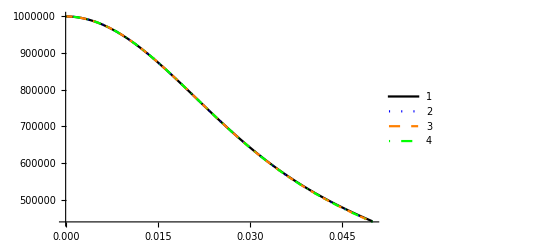

```mathematica
Plot[
{
1000 bd2b2[ga, gb, t]/.sol1,
100bd2b2[ga, gb, t]/.sol2,
10bd2b2[ga, gb, t]/.sol3,
bd2b2[ga, gb, t]/.sol4
},
{t,0,tmax2},
PlotLegends->{"1", "2", "3", "4"},
PlotStyle->{Black, {Dotted, Blue},{Dashed, Orange}, {DotDashed, Green}}
]
```

```mathematica
bd2b2[ga, gb, 0]/.sol4
```

1.×10^6+0. ⅈ

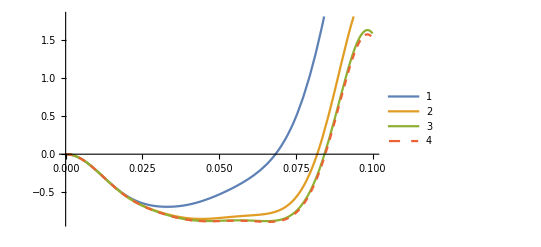

```mathematica
Plot[
{
Re@Qb2[ga, gb, t]/.sol1,
Re@Qb2[ga, gb, t]/.sol2,
Re@Qb2[ga, gb, t]/.sol3,
Re@Qb2[ga, gb, t]/.sol4
},
{t, 0, 0.1},
PlotLegends->{"1", "2", "3", "4"}
,PlotStyle->{,,,Dashed}
]
```

```mathematica
ga = 20
gb = 1/0.414 ga
gc = 3 * ga
```

20

48.3092

60

```mathematica
u=0.001;
sol = generalsolver2[0.0, u, putoa[100, u], 0.0, 11.5, 0.0, phogarray[ga, gb, gc, 5], 1];1;
```

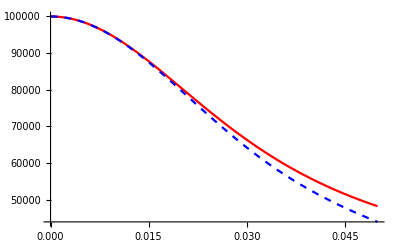

```mathematica
Plot[
{
bd2b2[ga, gb, t]/.sol,
bd2b2[ga, gb, t]/.sol3
},
{t,0,tmax2}
,PlotStyle->{Red, {Blue, Dashed}}
]
```

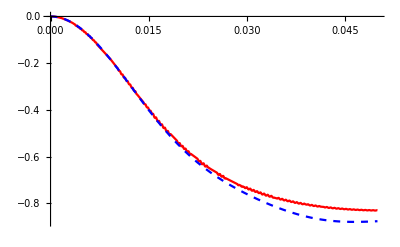

```mathematica
Plot[
{
Re@Qb2[ga, gb, t]/.sol,
Re@Qb2[ga, gb, t]/.sol3
},
{t, 0, tmax2},
PlotStyle->{Red, {Blue, Dashed}}
]
```

```mathematica
1/0.414*20
```

48.3092

```mathematica
ga=.
```

```mathematica
ga[gr_]:=gb * gr
gb = 50
gc = 60
```

50

60

```mathematica
ga[gr_]:=gb * gr
gb = 50
gc = 60
folder = NotebookDirectory[]<>"\\scanning\\n=10\\gb=50\\";
If[DirectoryQ[folder]==False, CreateDirectory[folder]];
SetDirectory[folder];
Export["testout.m", "hello"];
u=0.001;
Module[{out, pos, out2, file},
Table[
out =  generalsolver2[0.0, u, putoa[100, u], 0.0, 11.5, 0.0, phogarray[ga[r], gb, gc, 10], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}]; 
out2 = out[[pos]];
Export[ folder<>ToString[r]<>".mx",out2];
out=.
,{r, 0.1, 0.9, 0.05}
]

]
```

50

60

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
ga[gr_]:=gb * gr
gb = 30
gc = 60
folder = NotebookDirectory[]<>"\\scanning\\n=10\\gb=30\\";
If[DirectoryQ[folder]==False, CreateDirectory[folder]];
SetDirectory[folder];
Export["testout.m", "hello"];
u=0.001;
Module[{out, pos, out2, file},
Table[
out =  generalsolver2[0.0, u, putoa[100, u], 0.0, 11.5, 0.0, phogarray[ga[r], gb, gc, 10], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}]; 
out2 = out[[pos]];
Export[ folder<>ToString[r]<>".mx",out2];
out=.
,{r, 0.1, 0.9, 0.05}
]

]
```

30

60

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
ga[gr_]:=gb * gr
gb = 60
gc = 60
folder = NotebookDirectory[]<>"\\scanning\\n=10\\gb=60\\";
If[DirectoryQ[folder]==False, CreateDirectory[folder]];
SetDirectory[folder];
Export["testout.m", "hello"];
u=0.001;
Module[{out, pos, out2, file},
Table[
out =  generalsolver2[0.0, u, putoa[100, u], 0.0, 11.5, 0.0, phogarray[ga[r], gb, gc, 10], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}]; 
out2 = out[[pos]];
Export[ folder<>ToString[r]<>".mx",out2];
out=.
,{r, 0.1, 0.9, 0.05}
]

]
```

60

60

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

## Import and plot

```mathematica
folder = NotebookDirectory[]<>"\\scanning\\";
SetDirectory[folder]
```

C:\Users\MatthewThornton\OneDrive for Business\Year 3\PhoG\PhoG_paper\Calculations\scanning

```mathematica
import[n_,gb_, gr_]:=import[n, gb, gr] = 
Module[{file},
file = folder<>"n="<>ToString[n]<>"\\gb="<>ToString[gb]<>"\\"<>ToString[gr]<>".mx";
If[FileExistsQ[file],
Import[file],
Print["File does not exist"]; Abort[]
]
]
```

```mathematica
bd2b2[0.5*30, 30, 0.1]/.import[5, 30, 0.5]
```

22841.+0. ⅈ

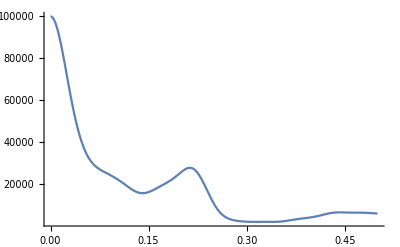

```mathematica
Plot[
Evaluate[bd2b2[0.5*30, 30, t]/.import[5, 30, 0.5]]
,
{t,0,0.5}, PlotRange->All
]
```

```mathematica
importlist530 = Table[
import[5, 30, gr],
{gr,grlist}
];1;
```

```mathematica
grlist = Table[gr, {gr, 0.1, 0.9, 0.05}];
```

```mathematica
importlist1030 = Table[
import[10, 30, gr],
{gr, grlist}
];1;
```

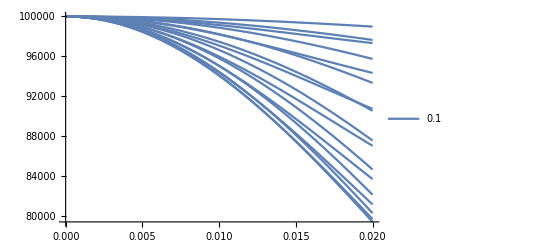

```mathematica
Plot[
Table[
Re@bd2b2[grlist[[i]] * 30, 30, t]/.importlist[[i]]
,{i, 1, Length[grlist]}
]
,
{t,0,0.02},
PlotLegends->(ToString[#]&/@grlist)
]
```

```mathematica
Length[grlist]
```

17

```mathematica
grlist
```

{0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9}

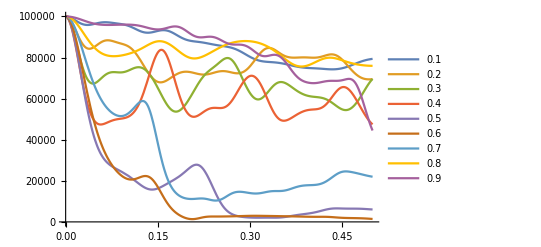

```mathematica
Plot[
{
Re@bd2b2[grlist[[1]] * 30, 30, t]/.importlist530[[1]],
Re@bd2b2[grlist[[3]] * 30, 30, t]/.importlist530[[3]],
Re@bd2b2[grlist[[5]] * 30, 30, t]/.importlist530[[5]],
Re@bd2b2[grlist[[7]] * 30, 30, t]/.importlist530[[7]],
Re@bd2b2[grlist[[9]] * 30, 30, t]/.importlist530[[9]],
Re@bd2b2[grlist[[11]] * 30, 30, t]/.importlist530[[11]],
Re@bd2b2[grlist[[13]] * 30, 30, t]/.importlist530[[13]],
Re@bd2b2[grlist[[15]] * 30, 30, t]/.importlist530[[15]],
Re@bd2b2[grlist[[17]] * 30, 30, t]/.importlist530[[17]]
},
{t, 0, 0.5}
, PlotLegends->{"0.1", "0.2", "0.3", "0.4", "0.5", "0.6", "0.7", "0.8", "0.9"}
]
```

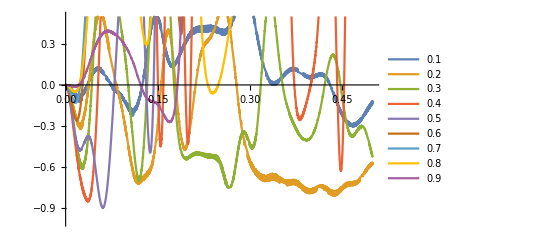

```mathematica
Plot[
{
Re@Qb2[grlist[[1]] * 30, 30, t]/.importlist530[[1]],
Re@Qb2[grlist[[3]] * 30, 30, t]/.importlist530[[3]],
Re@Qb2[grlist[[5]] * 30, 30, t]/.importlist530[[5]],
Re@Qb2[grlist[[7]] * 30, 30, t]/.importlist530[[7]],
Re@Qb2[grlist[[9]] * 30, 30, t]/.importlist530[[9]],
Re@Qb2[grlist[[11]] * 30, 30, t]/.importlist530[[11]],
Re@Qb2[grlist[[13]] * 30, 30, t]/.importlist530[[13]],
Re@Qb2[grlist[[15]] * 30, 30, t]/.importlist530[[15]],
Re@Qb2[grlist[[17]] * 30, 30, t]/.importlist530[[17]]
},
{t, 0, 0.5}
, PlotLegends->{"0.1", "0.2", "0.3", "0.4", "0.5", "0.6", "0.7", "0.8", "0.9"},
PlotRange->{-1,0.5}
]
```

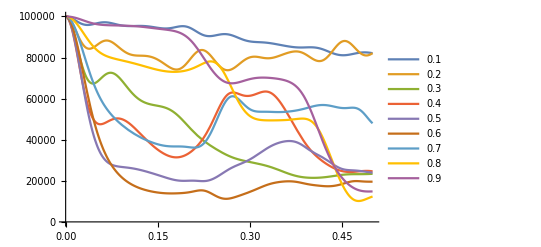

```mathematica
Plot[
{
Re@bd2b2[grlist[[1]] * 30, 30, t]/.importlist1030[[1]],
Re@bd2b2[grlist[[3]] * 30, 30, t]/.importlist1030[[3]],
Re@bd2b2[grlist[[5]] * 30, 30, t]/.importlist1030[[5]],
Re@bd2b2[grlist[[7]] * 30, 30, t]/.importlist1030[[7]],
Re@bd2b2[grlist[[9]] * 30, 30, t]/.importlist1030[[9]],
Re@bd2b2[grlist[[11]] * 30, 30, t]/.importlist1030[[11]],
Re@bd2b2[grlist[[13]] * 30, 30, t]/.importlist1030[[13]],
Re@bd2b2[grlist[[15]] * 30, 30, t]/.importlist1030[[15]],
Re@bd2b2[grlist[[17]] * 30, 30, t]/.importlist1030[[17]]
},
{t, 0, 0.5}
, PlotLegends->{"0.1", "0.2", "0.3", "0.4", "0.5", "0.6", "0.7", "0.8", "0.9"}
]
```

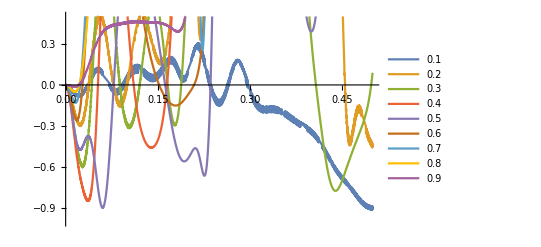

```mathematica
Plot[
{
Re@Qb2[grlist[[1]] * 30, 30, t]/.importlist1030[[1]],
Re@Qb2[grlist[[3]] * 30, 30, t]/.importlist1030[[3]],
Re@Qb2[grlist[[5]] * 30, 30, t]/.importlist1030[[5]],
Re@Qb2[grlist[[7]] * 30, 30, t]/.importlist1030[[7]],
Re@Qb2[grlist[[9]] * 30, 30, t]/.importlist1030[[9]],
Re@Qb2[grlist[[11]] * 30, 30, t]/.importlist1030[[11]],
Re@Qb2[grlist[[13]] * 30, 30, t]/.importlist1030[[13]],
Re@Qb2[grlist[[15]] * 30, 30, t]/.importlist1030[[15]],
Re@Qb2[grlist[[17]] * 30, 30, t]/.importlist1030[[17]]
},
{t, 0, 0.5}
, PlotLegends->{"0.1", "0.2", "0.3", "0.4", "0.5", "0.6", "0.7", "0.8", "0.9"},
PlotRange->{-1,0.5}
]
```

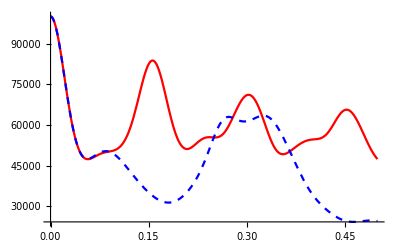

```mathematica
Plot[
{
bd2b2[grlist[[7]]*30, 30, t]/.importlist530[[7]],
bd2b2[grlist[[7]] * 30, 30, t]/.importlist1030[[7]]
},
{t,0,0.5},
PlotStyle->{Red, {Blue, Dashed}}
]
```

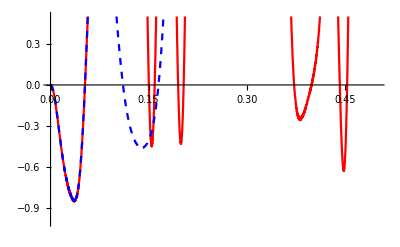

```mathematica
Plot[
{
Re@Qb2[grlist[[7]]*30, 30, t]/.importlist530[[7]],
Re@Qb2[grlist[[7]] * 30, 30, t]/.importlist1030[[7]]
},
{t,0,0.5},
PlotStyle->{Red, {Blue, Dashed}},
PlotRange->{-1,0.5}
]
```

```mathematica
importlist550 = Table[
import[5, 50, gr],
{gr,grlist}
];1;
importlist1050 = Table[
import[10, 50, gr],
{gr,grlist}
];1;
```

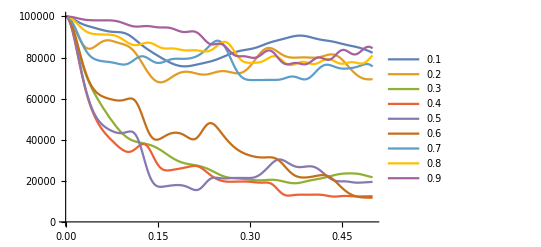

```mathematica
Plot[
{
Re@bd2b2[grlist[[1]] * 30, 30, t]/.importlist550[[1]],
Re@bd2b2[grlist[[3]] * 30, 30, t]/.importlist530[[3]],
Re@bd2b2[grlist[[5]] * 30, 30, t]/.importlist550[[5]],
Re@bd2b2[grlist[[7]] * 30, 30, t]/.importlist550[[7]],
Re@bd2b2[grlist[[9]] * 30, 30, t]/.importlist550[[9]],
Re@bd2b2[grlist[[11]] * 30, 30, t]/.importlist550[[11]],
Re@bd2b2[grlist[[13]] * 30, 30, t]/.importlist550[[13]],
Re@bd2b2[grlist[[15]] * 30, 30, t]/.importlist550[[15]],
Re@bd2b2[grlist[[17]] * 30, 30, t]/.importlist550[[17]]
},
{t, 0, 0.5}
, PlotLegends->{"0.1", "0.2", "0.3", "0.4", "0.5", "0.6", "0.7", "0.8", "0.9"}
]
```

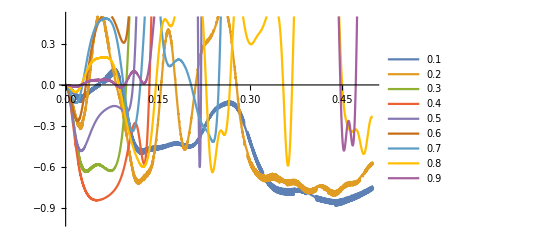

```mathematica
Plot[
{
Re@Qb2[grlist[[1]] * 30, 30, t]/.importlist550[[1]],
Re@Qb2[grlist[[3]] * 30, 30, t]/.importlist530[[3]],
Re@Qb2[grlist[[5]] * 30, 30, t]/.importlist550[[5]],
Re@Qb2[grlist[[7]] * 30, 30, t]/.importlist550[[7]],
Re@Qb2[grlist[[9]] * 30, 30, t]/.importlist550[[9]],
Re@Qb2[grlist[[11]] * 30, 30, t]/.importlist550[[11]],
Re@Qb2[grlist[[13]] * 30, 30, t]/.importlist550[[13]],
Re@Qb2[grlist[[15]] * 30, 30, t]/.importlist550[[15]],
Re@Qb2[grlist[[17]] * 30, 30, t]/.importlist550[[17]]
},
{t, 0, 0.5}
, PlotLegends->{"0.1", "0.2", "0.3", "0.4", "0.5", "0.6", "0.7", "0.8", "0.9"},
PlotRange->{-1,0.5}
]
```

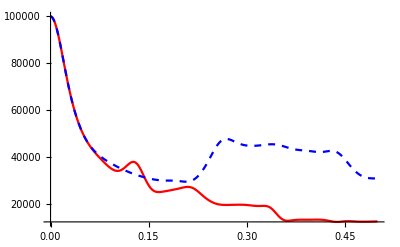

```mathematica
Plot[
{
bd2b2[grlist[[7]]*30, 30, t]/.importlist550[[7]],
bd2b2[grlist[[7]] * 30, 30, t]/.importlist1050[[7]]
},
{t,0,0.5},
PlotStyle->{Red, {Blue, Dashed}}
]
```

```mathematica
importlist560 = Table[
import[5, 60, gr],
{gr,grlist}
];1;
importlist1060 = Table[
import[10, 60, gr],
{gr,grlist}
];1;
```

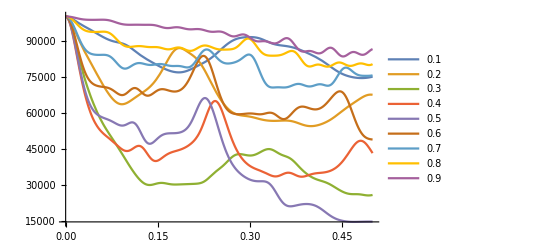

```mathematica
Plot[
{
Re@bd2b2[grlist[[1]] * 30, 30, t]/.importlist560[[1]],
Re@bd2b2[grlist[[3]] * 30, 30, t]/.importlist560[[3]],
Re@bd2b2[grlist[[5]] * 30, 30, t]/.importlist560[[5]],
Re@bd2b2[grlist[[7]] * 30, 30, t]/.importlist560[[7]],
Re@bd2b2[grlist[[9]] * 30, 30, t]/.importlist560[[9]],
Re@bd2b2[grlist[[11]] * 30, 30, t]/.importlist560[[11]],
Re@bd2b2[grlist[[13]] * 30, 30, t]/.importlist560[[13]],
Re@bd2b2[grlist[[15]] * 30, 30, t]/.importlist560[[15]],
Re@bd2b2[grlist[[17]] * 30, 30, t]/.importlist560[[17]]
},
{t, 0, 0.5}
, PlotLegends->{"0.1", "0.2", "0.3", "0.4", "0.5", "0.6", "0.7", "0.8", "0.9"}
]
```

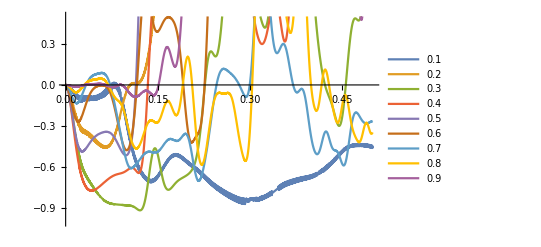

```mathematica
Plot[
{
Re@Qb2[grlist[[1]] * 30, 30, t]/.importlist560[[1]],
Re@Qb2[grlist[[3]] * 30, 30, t]/.importlist560[[3]],
Re@Qb2[grlist[[5]] * 30, 30, t]/.importlist560[[5]],
Re@Qb2[grlist[[7]] * 30, 30, t]/.importlist560[[7]],
Re@Qb2[grlist[[9]] * 30, 30, t]/.importlist560[[9]],
Re@Qb2[grlist[[11]] * 30, 30, t]/.importlist560[[11]],
Re@Qb2[grlist[[13]] * 30, 30, t]/.importlist560[[13]],
Re@Qb2[grlist[[15]] * 30, 30, t]/.importlist560[[15]],
Re@Qb2[grlist[[17]] * 30, 30, t]/.importlist560[[17]]
},
{t, 0, 0.5}
, PlotLegends->{"0.1", "0.2", "0.3", "0.4", "0.5", "0.6", "0.7", "0.8", "0.9"},
PlotRange->{-1,0.5}
]
```

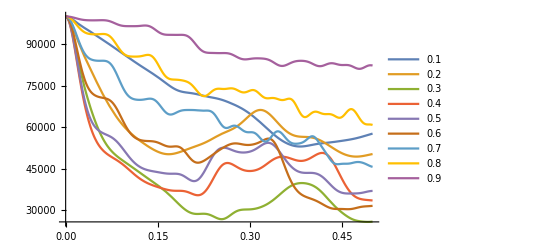

```mathematica
Plot[
{
Re@bd2b2[grlist[[1]] * 30, 30, t]/.importlist1060[[1]],
Re@bd2b2[grlist[[3]] * 30, 30, t]/.importlist1060[[3]],
Re@bd2b2[grlist[[5]] * 30, 30, t]/.importlist1060[[5]],
Re@bd2b2[grlist[[7]] * 30, 30, t]/.importlist1060[[7]],
Re@bd2b2[grlist[[9]] * 30, 30, t]/.importlist1060[[9]],
Re@bd2b2[grlist[[11]] * 30, 30, t]/.importlist1060[[11]],
Re@bd2b2[grlist[[13]] * 30, 30, t]/.importlist1060[[13]],
Re@bd2b2[grlist[[15]] * 30, 30, t]/.importlist1060[[15]],
Re@bd2b2[grlist[[17]] * 30, 30, t]/.importlist1060[[17]]
},
{t, 0, 0.5}
, PlotLegends->{"0.1", "0.2", "0.3", "0.4", "0.5", "0.6", "0.7", "0.8", "0.9"}
]
```

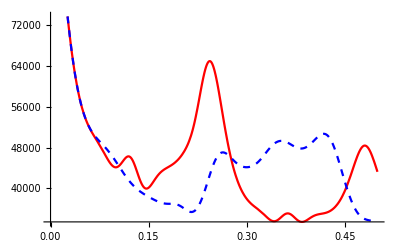

```mathematica
Plot[
{
bd2b2[grlist[[7]]*30, 30, t]/.importlist560[[7]],
bd2b2[grlist[[7]] * 30, 30, t]/.importlist1060[[7]]
},
{t,0,0.5},
PlotStyle->{Red, {Blue, Dashed}}
]
```

## Realistic signature behaviours

### Checking scaling

```mathematica
u = √((8*10^-18)/0.0011)
```

8.52803×10^-8

```mathematica
√(1.2*10^9)
```

34641.

```mathematica
700/500*1.2
```

1.68

```mathematica
300/500*1.2
```

0.72

```mathematica
100/500*1.2
```

0.24

```mathematica
pfun[u_, nin_]:=u * nin
```

```mathematica
pfun[u,1.7*10^9]
```

144.976

```mathematica
u * 1.2*10^9
```

102.336

```mathematica
putoa[20.5, 0.001]
```

143.178

```mathematica
(*generalsolver2[w_, U_, αin_, Γ_,Γn_, nthermal_,adjacencymatrix_,tmax_] *)
```

```mathematica
ga=.
gb=.
```

```mathematica
ga = 0.412 * 50;
gb  = 50;
gc = 60;
```

```mathematica
ufake = 0.001;
pfake = 145;
sol1 = generalsolver2[0.0, ufake, putoa[pfake, ufake], 11.5, 0.0, 0.0, phogarray[ga, gb, gc, 5], 1];1;
ufake=.
```

```mathematica
ufake = 0.0001;
sol2 = generalsolver2[0.0, ufake, putoa[pfake, ufake], 11.5, 0.0, 0.0, phogarray[ga, gb, gc, 5], 1];1;
ufake=.
```

```mathematica
putoa[pfake, 0.001]/putoa[pfake, 0.0001]
```

0.316228

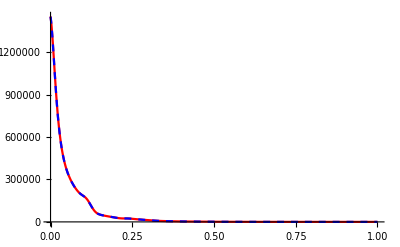

```mathematica
Plot[
{
1/0.316^2 bd2b2[ga, gb, t]/.sol1,
bd2b2[ga, gb, t]/.sol2
},
{t,0,1.0},
PlotStyle->{Red, {Blue, Dashed}}, PlotRange->All
]
```

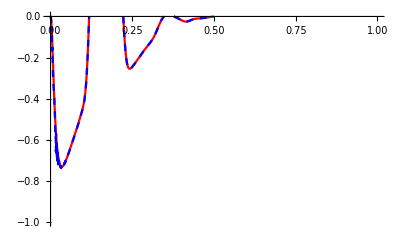

```mathematica
Plot[
{
Re@Qb2[ga, gb, t]/.sol1,
Re@Qb2[ga, gb, t]/.sol2
},
{t,0,1},
PlotStyle->{Red, {Blue, Dashed}}, PlotRange->{-1,0}
]
```

### Actual runs

```mathematica
u = √((8*10^-18)/0.0011)
ga = 0.412 * 50;
gb  = 50;
gc = 60;
```

8.52803×10^-8

```mathematica
folder = NotebookDirectory[]<>"\\realistic_runs\\";
If[DirectoryQ[folder],Null, CreateDirectory[folder]];
SetDirectory[folder]
```

C:\Users\MatthewThornton\OneDrive for Business\Year 3\PhoG\PhoG_paper\Calculations\realistic_runs

```mathematica
sol1=.
```

```mathematica
ufake = 0.001;
pfake = 62;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], 0.0, 0.0, 0.0, phogarray[ga, gb, gc, 10], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=62.N=10"<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
pfake = 21;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], 0.0, 0.0, 0.0, phogarray[ga, gb, gc, 10], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=21.N=10"<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
pfake = 102;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], 0.0, 0.0, 0.0, phogarray[ga, gb, gc, 10], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=102.N=10"<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
pfake = 145;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], 0.0, 0.0, 0.0, phogarray[ga, gb, gc, 5], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=145.N=5"<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
sol21 =  generalsolver2[0.0, 0, putoa[21, ufake], 11.5, 0.0, 0.0, phogarray[ga, gb, gc, 5], 1];1;
sol62 = generalsolver2[0.0, 0, putoa[62, ufake], 11.5, 0.0, 0.0, phogarray[ga, gb, gc, 5], 1];1;
sol102 = generalsolver2[0.0, 0, putoa[102, ufake], 11.5, 0.0, 0.0, phogarray[ga, gb, gc, 5], 1];
sol145 = generalsolver2[0.0, 0, putoa[145, ufake], 11.5, 0.0, 0.0, phogarray[ga, gb, gc, 5], 1]1;
ufake=.
```

### Importing and plotting

```mathematica
soln5p21 = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\p=21.N=5.mx"];
soln5p62 = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\p=62.N=5.mx"];
soln5p102 = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\p=102.N=5.mx"];
soln5p145= Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\p=145.N=5.mx"];

soln10p21 = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\p=21.N=10.mx"];
soln10p62 = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\p=62.N=10.mx"];
soln10p102 = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\p=102.N=10.mx"];
soln10p145= Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\p=145.N=10.mx"];
```

```mathematica
bd2b2[ga, gb, 0.1]/.soln5p145
```

0.000341955 (2500 ad1a1[0.1]-1030. ad1a2[0.1]-1030. ad2a1[0.1]+424.36 ad2a2[0.1])/.$Failed

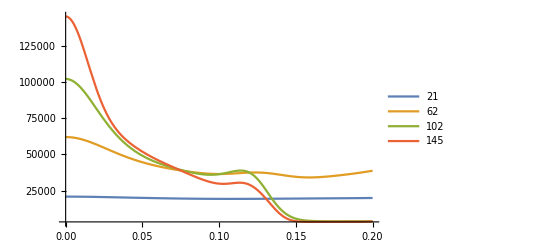

```mathematica
Plot[
{
bd2b2[ga, gb, t]/.soln5p21,
bd2b2[ga, gb, t]/.soln5p62,
bd2b2[ga, gb, t]/.soln5p102,
bd2b2[ga, gb, t]/.soln5p145
},
{t,0,0.2},
PlotLegends->{"21", "62", "102", "145"}, 
PlotRange->All
]
```

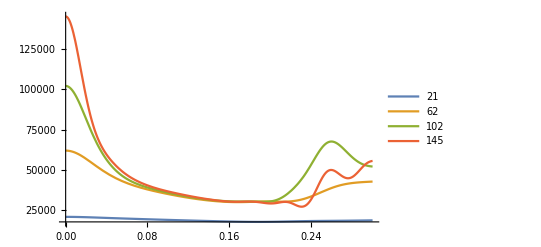

```mathematica
Plot[
{
bd2b2[ga, gb, t]/.soln10p21,
bd2b2[ga, gb, t]/.soln10p62,
bd2b2[ga, gb, t]/.soln10p102,
bd2b2[ga, gb, t]/.soln10p145
},
{t,0,0.3},
PlotLegends->{"21", "62", "102", "145"}, 
PlotRange->All
]
```

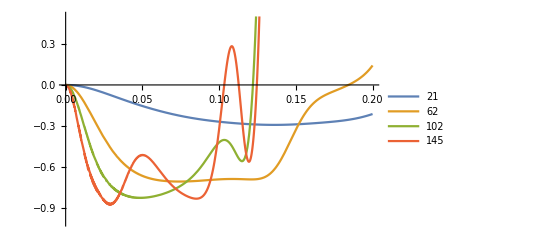

```mathematica
Plot[
{
Re@Qb2[ga, gb, t]/.soln5p21,
Re@Qb2[ga, gb, t]/.soln5p62,
Re@Qb2[ga, gb, t]/.soln5p102,
Re@Qb2[ga, gb, t]/.soln5p145
},
{t,0,0.2},
PlotLegends->{"21", "62", "102", "145"}, 
PlotRange->{-1,0.5}
]
```

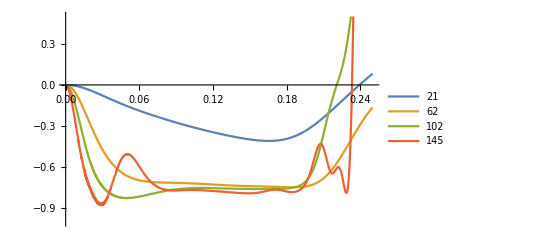

```mathematica
Plot[
{
Re@Qb2[ga, gb, t]/.soln10p21,
Re@Qb2[ga, gb, t]/.soln10p62,
Re@Qb2[ga, gb, t]/.soln10p102,
Re@Qb2[ga, gb, t]/.soln10p145
},
{t,0,0.25},
PlotLegends->{"21", "62", "102", "145"}, 
PlotRange->{-1,0.5}
]
```

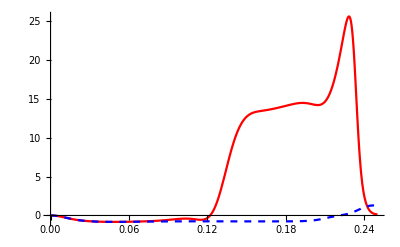

```mathematica
Plot[
{
Re@Qb2[ga, gb, t]/.soln5p102,
Re@Qb2[ga, gb, t]/.soln10p102
}
,
{t,0,0.25},
PlotStyle->{Red, {Blue, Dashed}}
]
```

#### Some runs varying γ1 - nmodes=5

```mathematica
ufake = 0.001;
pfake = 102;
γ1 = 0.0;
nmodes = 5;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"gamma1="<>ToString[γ1]<>".N="<>ToString[nmodes]<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
pfake = 102;
γ1 = 11.5;
nmodes = 5;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"gamma1="<>ToString[γ1]<>".N="<>ToString[nmodes]<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
pfake = 102;
γ1 = 20.0;
nmodes = 5;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"gamma1="<>ToString[γ1]<>".N="<>ToString[nmodes]<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
pfake = 102;
γ1 = 200.0;
nmodes = 5;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"gamma1="<>ToString[γ1]<>".N="<>ToString[nmodes]<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
pfake = 102;
γ1 = 400.0;
nmodes = 5;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"gamma1="<>ToString[γ1]<>".N="<>ToString[nmodes]<>".mx",out2];
]
ufake=.
pfake=.
```

#### Some runs varying γ1 - nmodes=10

```mathematica
ufake = 0.001;
pfake = 102;
γ1 = 0.0;
nmodes = 10;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"gamma1="<>ToString[γ1]<>".N="<>ToString[nmodes]<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
pfake = 102;
γ1 = 11.5;
nmodes = 10;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"gamma1="<>ToString[γ1]<>".N="<>ToString[nmodes]<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
pfake = 102;
γ1 = 20.0;
nmodes = 10;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"gamma1="<>ToString[γ1]<>".N="<>ToString[nmodes]<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
pfake = 102;
γ1 = 200.0;
nmodes = 10;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"gamma1="<>ToString[γ1]<>".N="<>ToString[nmodes]<>".mx",out2];
]
ufake=.
pfake=.
```

```mathematica
ufake = 0.001;
pfake = 102;
γ1 = 400.0;
nmodes = 10;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"gamma1="<>ToString[γ1]<>".N="<>ToString[nmodes]<>".mx",out2];
]
ufake=.
pfake=.
```

#### Importing and plotting

```mathematica
soln5gam0=Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\gamma1=0..N=5.mx"];1;
soln5gam115=Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\gamma1=11.5.N=5.mx"];1;
soln5gam20=Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\gamma1=20..N=5.mx"];1;
soln5gam200=Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\gamma1=200..N=5.mx"];1;
soln5gam400=Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\gamma1=400..N=5.mx"];1;

soln10gam0=Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\gamma1=0..N=10.mx"];1;
soln10gam115=Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\gamma1=11.5.N=10.mx"];1;
soln10gam20=Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\gamma1=20..N=10.mx"];1;
soln10gam200=Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\gamma1=200..N=10.mx"];1;
soln10gam400=Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\gamma1=400..N=10.mx"];1;
```

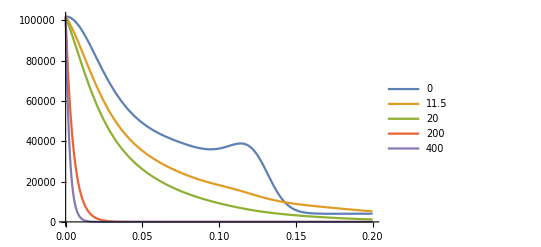

```mathematica
Plot[
{
bd2b2[ga, gb, t]/.soln5gam0,
bd2b2[ga, gb, t]/.soln5gam115,
bd2b2[ga, gb, t]/.soln5gam20,
bd2b2[ga, gb, t]/.soln5gam200,
bd2b2[ga, gb, t]/.soln5gam400
},
{t,0,0.2}
,
PlotLegends->{"0", "11.5", "20", "200", "400"}
]
```

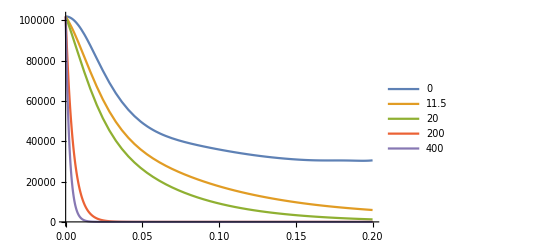

```mathematica
Plot[
{
bd2b2[ga, gb, t]/.soln10gam0,
bd2b2[ga, gb, t]/.soln10gam115,
bd2b2[ga, gb, t]/.soln10gam20,
bd2b2[ga, gb, t]/.soln10gam200,
bd2b2[ga, gb, t]/.soln10gam400
},
{t,0,0.2}
,
PlotLegends->{"0", "11.5", "20", "200", "400"}
]
```

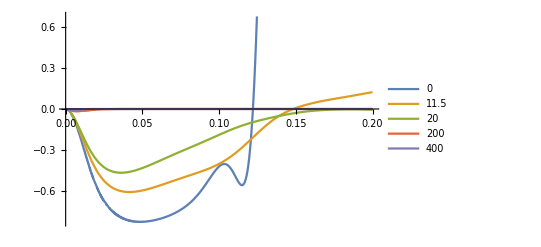

```mathematica
Plot[
{
Re@Qb2[ga, gb, t]/.soln5gam0,
Re@Qb2[ga, gb, t]/.soln5gam115,
Re@Qb2[ga, gb, t]/.soln5gam20,
Re@Qb2[ga, gb, t]/.soln5gam200,
Re@Qb2[ga, gb, t]/.soln5gam400
},
{t,0,0.2}
,
PlotLegends->{"0", "11.5", "20", "200", "400"}
]
```

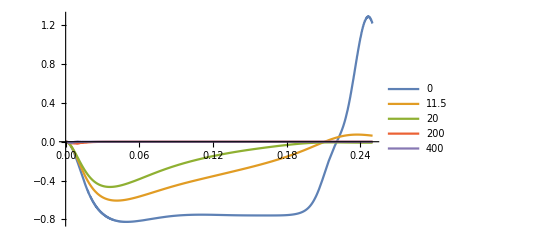

```mathematica
Plot[
{
Re@Qb2[ga, gb, t]/.soln10gam0,
Re@Qb2[ga, gb, t]/.soln10gam115,
Re@Qb2[ga, gb, t]/.soln10gam20,
Re@Qb2[ga, gb, t]/.soln10gam200,
Re@Qb2[ga, gb, t]/.soln10gam400
},
{t,0,0.25}
,
PlotLegends->{"0", "11.5", "20", "200", "400"}
]
```

### No scaling

```mathematica
ufake = 8.52*10^-8;
ain = 34641
nmodes=5;
γ1=0;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, ain, γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"no_scaling_gamma1="<>ToString[γ1]<>"_nmodes="<>ToString[nmodes]<>".mx",out2];
]
ufake=.
ain=.
γ1=.
nmodes=.
```

34641

```mathematica
sol = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\no_scaling_gamma1=0_nmodes=5.mx"];1;
```

```mathematica
solscaled = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\varying_ain\\gamma1=0\\p=102.N=5.mx"];1;
```

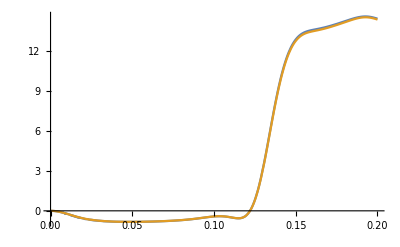

```mathematica
Plot[{
Re@Qb2[ga, gb, t]/.sol,
Re@Qb2[ga, gb, t]/.solscaled
}
,
{t,0,0.2}
]
```

### Large N runs

p=21

```mathematica
γ1=11.5;
pfake=21;
ufake=0.001;
```

```mathematica
nmodes = 10;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=24.N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 15;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=24.N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 20;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=24.N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 30;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=24.N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

#### p=62

```mathematica
γ1=11.5;
ufake=0.001;
pfake=62;
```

```mathematica
nmodes = 10;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 15;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 20;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 30;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
γ1=.
pfake=.
ufake=.
```

#### p=102

```mathematica
γ1=11.5;
ufake=0.001;
pfake=102;
```

```mathematica
nmodes = 10;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 15;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 20;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 30;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
γ1=.
pfake=.
ufake=.
```

### Large N runs

p=21

```mathematica
γ1=11.5;
pfake=21;
ufake=0.001;
```

```mathematica
nmodes = 10;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=24.N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 15;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=24.N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 20;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=24.N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 30;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=24.N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

#### p=62

```mathematica
γ1=11.5;
ufake=0.001;
pfake=62;
```

```mathematica
nmodes = 10;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 15;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 20;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 30;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
γ1=.
pfake=.
ufake=.
```

#### p=145

```mathematica
γ1=11.5;
ufake=0.001;
pfake=145;
```

```mathematica
nmodes = 10;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 15;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 20;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
nmodes = 30;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p="<>ToString[pfake]<>".N="<>ToString[nmodes]<>".mx",out2];
]
nmodes=.
```

```mathematica
γ1=.
pfake=.
ufake=.
```

### Plotting

```mathematica
sol21 = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\Large_nmodes\\gamma1=0.0\\p=21.N=30.mx"];1;
sol62 = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\Large_nmodes\\gamma1=0.0\\p=62.N=30.mx"];1;
sol102 = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\Large_nmodes\\gamma1=0.0\\p=102.N=30.mx"];1;
sol145 = Import["C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\Large_nmodes\\gamma1=0.0\\p=145.N=30.mx"];1;
```

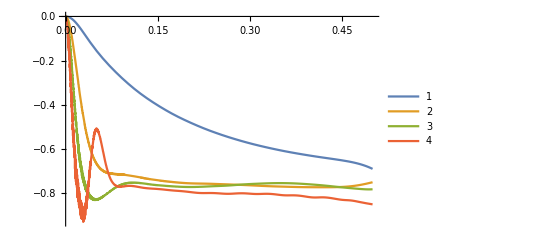

```mathematica
Plot[
{
Re@Qb2[ga, gb, t]/.sol21,
Re@Qb2[ga, gb, t]/.sol62,
Re@Qb2[ga, gb, t]/.sol102,
Re@Qb2[ga, gb, t]/.sol145
},
{t,0,0.5},
PlotLegends->Automatic
]
```

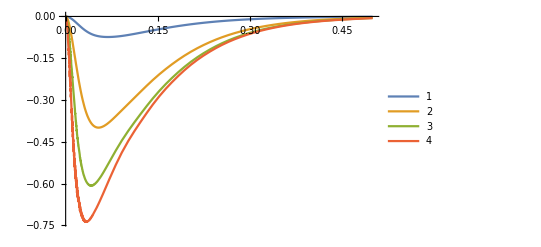

```mathematica
Plot[
{
Re@Qb2[ga, gb, t]/.sol21,
Re@Qb2[ga, gb, t]/.sol62,
Re@Qb2[ga, gb, t]/.sol102,
Re@Qb2[ga, gb, t]/.sol145
},
{t,0,0.5},
PlotLegends->Automatic
]
```

## Some more runs

```mathematica
nmodes = 30;

pfake=102;
ufake=0.001;
```

```mathematica
γ1=0.0;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=102.N=30.gamma1="<>ToString[γ1]<>".mx",out2];
]
γ1=.
```

```mathematica
γ1=11.5;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=102.N=30.gamma1="<>ToString[γ1]<>".mx",out2];
]

γ1=.
```

```mathematica
γ1=20.0;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=102.N=30.gamma1="<>ToString[γ1]<>".mx",out2];
]

γ1=.
```

```mathematica
γ1=40.0;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=102.N=30.gamma1="<>ToString[γ1]<>".mx",out2];
]
γ1=.
```

```mathematica
nmodes=.
pfake=.
ufake=.
```

## Larger precision p=145 and p=102

```mathematica
ga
```

20.6

```mathematica
gb
```

50

```mathematica
gc
```

60

```mathematica
pfake = 145;
γ1=0.0
nmodes = 5;
soltest = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
```

0.

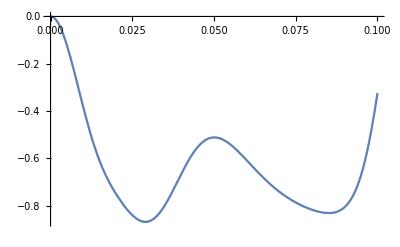

```mathematica
Plot[
{
Re@Qb2[ga, gb, t]/.soltest
},
{t,0,0.1}
]
```

```mathematica
folder = "C:\\Users\\MatthewThornton\\OneDrive for Business\\Year 3\\PhoG\\PhoG_paper\\Calculations\\realistic_runs\\";
```

```mathematica
pfake=145;
ufake=0.001;
γ1=0.0;
nmodes=15;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=145.N=15.gamma1="<>ToString[γ1]<>".mx",out2];
]
```

```mathematica
pfake=145;
ufake=0.001;
γ1=11.5;
nmodes=15;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=145.N=15.gamma1="<>ToString[γ1]<>".mx",out2];
]
```

```mathematica
pfake=102;
ufake=0.001;
γ1=0.0;
nmodes=15;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=102.N=15.gamma1="<>ToString[γ1]<>".mx",out2];
]
```

```mathematica
pfake=102;
ufake=0.001;
γ1=11.5;
nmodes=15;
Module[{out, pos, out2, file},
out = generalsolver2[0.0, ufake, putoa[pfake, ufake], γ1, 0.0, 0.0, phogarray[ga, gb, gc, nmodes], 1];1;
pos=Table[Position[out,thingsicareabout[[i]]][[1,1]],{i,1,Length[thingsicareabout]}];
out2 = out[[pos]];
Export[ folder<>"p=102.N=15.gamma1="<>ToString[γ1]<>".mx",out2];
]
```